```mathematica
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
ySep=1.75;
aLen=0.65;
```

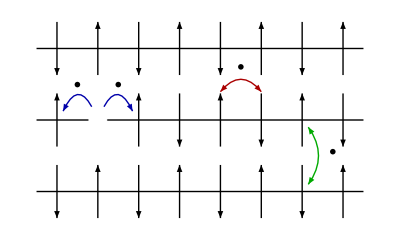

```mathematica
chains3=Graphics[{
Black,Thick,Line[{{-1.5,ySep},{6.5,ySep}}],
Black,Thick,Line[{{-1.5,0},{6.5,0}}],
Black,Thick,Line[{{-1.5,-ySep},{6.5,-ySep}}],
EdgeForm[Thick],White,Disk[{0,0},aLen/3],
Black,Thick,Arrowheads[0.05],
Arrow[{{-1,-aLen},{-1,aLen}}],
Arrow[{{1,-aLen},{1,aLen}}],
Arrow[{{2,aLen},{2,-aLen}}],
Arrow[{{3,-aLen},{3,aLen}}],
Arrow[{{4,aLen},{4,-aLen}}],
Arrow[{{5,-aLen},{5,aLen}}],
Arrow[{{6,aLen},{6,-aLen}}],
Arrow[{{-1,aLen+ySep},{-1,-aLen+ySep}}],
Arrow[{{0,-aLen+ySep},{0,aLen+ySep}}],
Arrow[{{1,aLen+ySep},{1,-aLen+ySep}}],
Arrow[{{2,-aLen+ySep},{2,aLen+ySep}}],
Arrow[{{3,aLen+ySep},{3,-aLen+ySep}}],
Arrow[{{4,-aLen+ySep},{4,aLen+ySep}}],
Arrow[{{5,aLen+ySep},{5,-aLen+ySep}}],
Arrow[{{6,-aLen+ySep},{6,aLen+ySep}}],
Arrow[{{-1,aLen-ySep},{-1,-aLen-ySep}}],
Arrow[{{0,-aLen-ySep},{0,aLen-ySep}}],
Arrow[{{1,aLen-ySep},{1,-aLen-ySep}}],
Arrow[{{2,-aLen-ySep},{2,aLen-ySep}}],
Arrow[{{3,aLen-ySep},{3,-aLen-ySep}}],
Arrow[{{4,-aLen-ySep},{4,aLen-ySep}}],
Arrow[{{5,aLen-ySep},{5,-aLen-ySep}}],
Arrow[{{6,-aLen-ySep},{6,aLen-ySep}}],
Darker[Blue],Thick,Arrowheads[0.04],
Arrow[BezierCurve[{{0.15,aLen/2},{0.5,3aLen/2},{0.85,aLen/3}}]],
Arrow[BezierCurve[{{-0.15,aLen/2},{-0.5,3aLen/2},{-0.85,aLen/3}}]],
Darker[Red],Thick,Arrowheads[{-0.04,0.04}],
Arrow[BezierCurve[{{3,16aLen/15},{3.5,2aLen},{4,16aLen/15}}]],
Darker[Green],Thick,Arrowheads[{-0.04,0.04}],
Arrow[BezierCurve[{{5.15,0.1 ySep-ySep},{5.65 ,ySep/2-ySep},{5.15,0.9ySep-ySep}}]]
},
Epilog->{
Inset[MaTeX["t",Magnification->2],{0.5,4aLen/3}],
Inset[MaTeX["t",Magnification->2],{-0.5,4aLen/3}],
Inset[MaTeX["J",Magnification->2],{3.5,2aLen}],
Inset[MaTeX["J_\\perp",Magnification->2],{5.75,-ySep/2+0.1}]
}
]
```

```mathematica
Export["plots/chains3.png",chains3,ImageResolution->300];
```